```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\factorial_cumulant\resonancegas

```mathematica
STARFit1=Flatten[Import["../freezeout/freezeout/STARFitI.dat"]];
STARFit2=Flatten[Import["../freezeout/freezeout/STARFitII.dat"]];
mubfre=Flatten[Import["../freezeout/freezeout/mub.dat"]];
```

```mathematica
HRGchi1=Table[chi[1,0,0][STARFit2[[i]],mubfre[[i]],0,0],{i,1,160}];
HRGchi2=Table[chi[2,0,0][STARFit2[[i]],mubfre[[i]],0,0],{i,1,160}];
```

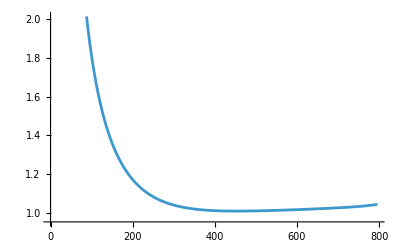

```mathematica
ListLinePlot[{Transpose[{mubfre,HRGchi2/HRGchi1}]}]
```

```mathematica
Export["R21HRGII.dat",HRGchi2/HRGchi1]
```

R21HRGII.dat